# u_xx= ⅇ^u

## relaxation code

numerics

## preliminaries

### import eoms

```mathematica
Eq = D[ u[y], y, y ] - Exp[ u[y] ];
```

### grids

```mathematica
Off[Part::pkspec1]
Off[LinearSolve::luc]
```

#### Cheb grid and d1

```mathematica
ChebGrid[xp_,xm_,nn_]:= Module[{ys,a,diag,d1,d2} ,

ys = Table[1/2(xp + xm) + 1/2(xp - xm) Cos[(π (i-1))/nn], {i,1,nn+1}];
d1= NDSolve`FiniteDifferenceDerivative[Derivative[1],{ys},"DifferenceOrder"->"Pseudospectral"]["DifferentiationMatrix"];
d2= NDSolve`FiniteDifferenceDerivative[Derivative[2],{ys},"DifferenceOrder"->"Pseudospectral"]["DifferentiationMatrix"];

{ys,d1,d2}

];
```

### input eoms

```mathematica
eqaux[0]=Eq;
eqaux[1]=u[y];
eqaux[2]=u[y];
```

```mathematica
RepLin = {u-> Function[{y},  ϕ0[y] + ϵ  δϕ[y] ]};
 
For[ i=0,i≤ 2,i++,
EqApprox[i]= eqaux[i]/. RepLin;
eqlin[i]= D[EqApprox[i], ϵ] /. ϵ->0;
J[i]=  - EqApprox[i] /. ϵ->0;
];

Clear[i]
```

### module to compute the coefficients

```mathematica
ParseCoeffModule[nn_][ub_]:= Module[ {u,ubflat, Coeff, CoeffSymbolic, JCoeffSymbolic,CoeffData,JCoeffData,JCoeff,rep1,i,j,k,l,p,reps, ysT,d1y,d2y,repAUX},

(* evaluate the grid and derivatives *)
reps = {};
{ysT, d1y,d2y}= ChebGrid[-1.,1.,nn];

(* Read off coefficients *)
For[ i=0,i≤ 2,i++,
(* [derivative][bndy location]  *)
	        Coeff[3][i]= D[eqlin[i], D[D[δϕ[y], y], y]] /. reps;
	        Coeff[2][i]= D[eqlin[i], D[δϕ[y], y]] /.reps;
	        Coeff[1][i]= D[eqlin[i], δϕ[y] ]/. reps ;

JCoeff[i]= J[i]/. reps;

];

(* replacements for background configuration. rename derivatives and call them as different functions *)
       u[1] = ub  /. reps;
u[2] =  d1y.ub /. reps;
u[3] =  d2y.ub /. reps;
       rep1= {ϕ0''[y]-> u[3],ϕ0'[y]-> u[2] ,ϕ0[y]-> u[1]};
repAUX = Dispatch[ Flatten[ {rep1, y-> ysT} ] ];

(* evaluate the different pieces on the grid points. need to include the product with the array of 1 in case the result for the coefficient is 0 *)
CoeffSymbolic = Table[ Evaluate[ Coeff[i][j]/. repAUX  ]*ConstantArray[1.,nn+1],{i,1,3} , {j,0,2}];
JCoeffSymbolic = Table[Evaluate[ JCoeff[j] /. repAUX ]*SparseArray[ConstantArray[1.,nn+1]], {j,0,2}] ;

{ CoeffSymbolic,JCoeffSymbolic } 

];
```

### module to implement bcs

```mathematica
DataWithBc[nn_][CoeffData_]:= Module[{CoeffDataBC},

CoeffDataBC = CoeffData[[1]];
CoeffDataBC[[1]]= CoeffData[[2,1]];
CoeffDataBC[[nn+1]]= CoeffData[[3,nn+1]];

CoeffDataBC

];
```

### module to solve the linear problem

```mathematica
LinSolve[nn_][ub_]:= Module[ {AllCoeff,L2,J2,l,p,ParseCoeffAux,ysT,d1y,d2y,Id}, 

(* call module which computes coefficients *)
ParseCoeffAux =ParseCoeffModule[nn][ub];

(* evaluate grid *)
{ysT, d1y,d2y}= ChebGrid[-1.,1.,nn];
Id = N[IdentityMatrix[nn+1]];

(* impose bcs *)
AllCoeff[1] =   DataWithBc[nn][ParseCoeffAux[[1,1]]];
AllCoeff[2] =   DataWithBc[nn][ParseCoeffAux[[1,2]]];
AllCoeff[3] =   DataWithBc[nn][ParseCoeffAux[[1,3]]];

(* assemble full linear operator and source *)
L2 = AllCoeff[3]*d2y + AllCoeff[2]*d1y + AllCoeff[1]*Id; 
J2 = DataWithBc[nn][ParseCoeffAux[[2]]];

(* solve linear problem *)
LinearSolve[L2,J2]

 ];
```

### evaluate equation

```mathematica
ValEq[nn_][ub_]:= Module[{EqEval,rep1,ubflat,χ,l,ySaux,mder,ysT,d1y,d2y,reps,repAUX}, 

(* evaluate grid and derivatives *)
reps = {};
{ysT, d1y,d2y}= ChebGrid[-1.,1.,nn];

(* evaluate background and its derivatives *)
        χ[1] = ub /. reps;
        χ[2] =  d1y.ub /. reps;
 χ[3] =  d2y.ub /. reps;

(* create replacement rules *)
rep1= {ϕ0''[y]-> χ[3],ϕ0'[y]-> χ[2],ϕ0[y]-> χ[1]};
repAUX = Dispatch[ Flatten[ {rep1,  y-> ysT} ]] ;

(* evaluate bulk eom *)
EqEval= eqaux[0]/.{u-> Function[{y},  ϕ0[y] ]}   /. repAUX  /. reps ;

(* select pieces which do not involve the boundary  *)
EqEval[[2;;-2]]

];
```

### NR

```mathematica
NR[nn_][seed_][imax_]:= Module[{u, Δu,i,error,convergence}, 

u = seed;
error = 10^6;
convergence= 100;

For[i=1, i≤ imax &&  Or[ convergence > 10^-6 ,  10^-8 < error  <  10^8 ], i++ , 

Δu = LinSolve[nn][u];
u = u + Δu;

error = Max[ Abs[ ValEq[nn][u] ]];
convergence = Max[Abs[Δu]] ;
Print[{convergence, error}]

];

If[ error< 10^8, {u,Δu, error} , Break[]; ]

];
```

## solution

```mathematica
Test1 = NR[30][ConstantArray[1., 31]][5][[1]]; // AbsoluteTiming
```

{1.,1.}

{0.351946,0.055264}

{0.0160854,0.0000905022}

{0.0000249178,2.14849×10^-10}

{5.83699×10^-11,1.62426×10^-13}

{0.010011,Null}

```mathematica
DataToPlot[ub_]:= Module[{ysT, d1y,d2y, nn}, 

nn = Length[ub] -1 ;
{ysT, d1y,d2y}= ChebGrid[-1.,1.,nn];

Table[ { ysT[[i]], ub[[i]]  }, {i, 1, nn+1} ]

];
```

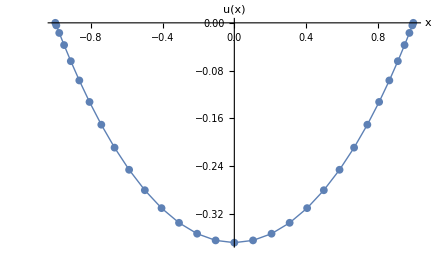

```mathematica
Show[ ListPlot[ DataToPlot[Test1] , AxesLabel->{"x","u(x)"}, BaseStyle->16], ListLinePlot[ DataToPlot[Test1] , PlotStyle->Thin] ]
```

```mathematica
Select[ DataToPlot[Test1], #[[1]] == 0 & ][[1,2]]
```

-0.368056